```mathematica
SetDirectory@NotebookDirectory[];
Import["QLanczos_package.m"];
```

## Parameters

```mathematica
d=5;
Id=IdentityMatrix[d];
η=1.5*10.^-15;(*machine precision*)
```

```mathematica
ηList=Table[10.^j,{j,-15,5,0.1}];
```

## Model

```mathematica
Ham=HeisenbergHam;
```

## Spectrum

```mathematica
{Λ,U}=funSpectrum[Ham];
HamNorm=Max[Abs[Λ]]
Λ=Λ/HamNorm;
Eg=Λ[[1]]
```

17.0321

-1.

```mathematica
htot=27./HamNorm
```

1.58524

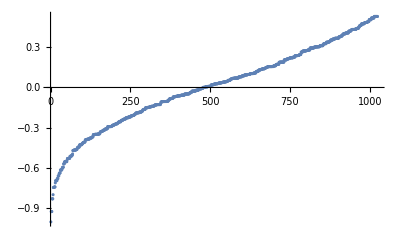

```mathematica
ListPlot[Λ,PlotRange->Full]
```

## Reference state

```mathematica
φ=φHeisenberg;
φ=Flatten[Conjugate[U].φ];
probφ=Abs[φ]^2;
```

```mathematica
pg=probφ[[1]](*pg>10^-3*)
ER=Total[probφ*Λ];
ϵR=ER-Eg
```

0.682614

0.119312

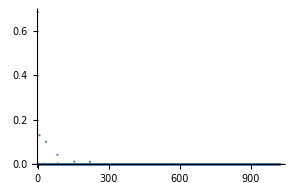

```mathematica
ListPlot[probφ,PlotRange->Full]
```

## Gaussian-Power with different tau

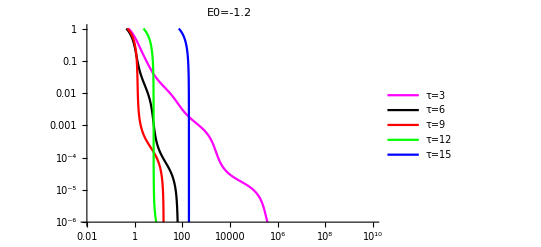

```mathematica
costH=htot;
costS=1;
E0=Eg-0.2;
τList=Table[i,{i,3,15,3}];
τCurves={};
Do[
τ=τList[[j]];
{Hmat,Smat}=funMatGP[Λ,E0,τ,d,probφ,htot];
{ϵList,γList}=funEpsilonGamma[Hmat,Smat,costH,costS,Id,ηList,Eg,pg];
AppendTo[τCurves,Transpose[{γList,ϵList}]];
,{j,1,Length[τList]}];
PR={{1.*^-2,1.*^10},{1.*^-6,1.*^0}};
ListLogLogPlot[τCurves,PlotStyle->{Magenta,Black,Red,Green,Blue},PlotLegends->{"τ=3","τ=6","τ=9","τ=12","τ=15"},PlotRange->PR,Joined->True,PlotLabel->"E0=-1.2"]
```

## Gaussian-Power as a filter

```mathematica
funGassianPower[k_,τ_,xList_,htot_,d_]:=Module[{x,yList,costList},
costList=funCost[htot,τ,d];
yList=0*xList;
Do[
x=xList[[i]];
If[k==1,
yList[[i]]=Exp[-x^2τ^2/2]/costList[[k]];
,yList[[i]]=Abs[x^(k-1)*Exp[-x^2τ^2/2]]/costList[[k]](*(((k-1)/(E τ^2))^((k-1)/2))*)
]
,{i,1,Length[xList]}];
yList]
```

```mathematica
τ=5;
xList=Table[i,{i,-1,1,0.005}];
```

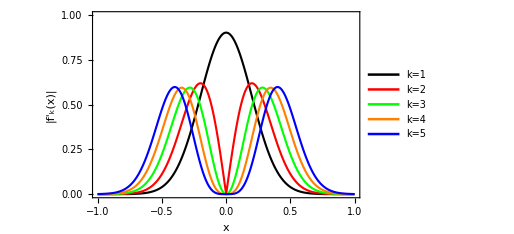

```mathematica
ListPlot[{Transpose[{xList,funGassianPower[1,τ,xList,htot,d]}],Transpose[{xList,funGassianPower[2,τ,xList,htot,d]}],Transpose[{xList,funGassianPower[3,τ,xList,htot,d]}],Transpose[{xList,funGassianPower[4,τ,xList,htot,d]}],Transpose[{xList,funGassianPower[5,τ,xList,htot,d]}]},(*GridLines->{{Sqrt[k-1]/τ},{((k-1)/(E τ^2))^((k-1)/2)}},*)PlotRange->{{-1,1},{0,1}},PlotStyle->{{Thickness[0.004],Black},{Thickness[0.004],Red},{Thickness[0.004],Green},{Thickness[0.004],Orange},{Thickness[0.004],Blue}},Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"x","|f'_k(x)|"},PlotLegends->Placed[LineLegend[{"k=1","k=2","k=3","k=4","k=5"},LegendFunction->(Framed[#,FrameStyle->LightGray]&),LegendMarkerSize->{16,8},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Times New Roman"},LegendMargins->0,LegendLayout->{"Column",1}],{0.9,0.7}],LabelStyle->{FontSize->15,FontFamily->"Arial"},ImageSize->380]
```